# Mandelbrot Set

The Mandelbrot set 
	https://en.wikipedia.org/wiki/Mandelbrot_set
  is ℳ={c∈ℂ: z_(n+1)=z_n^2+c with z_0=0 does NOT have |z_n| →∞} note ℳ⊂ℂ.

This sort of suggests that for lots of values of c the sequence does go to ∞.   For me (if ℳ is interesting) it also produces lots of questions:
1) What about if I start form somewhere other than z_0=0?
2) What about other parameterized functions?  Suppose I replace f(z)=z^2+c with f(z)=2 cos(z)+c or f(z)=z^3/(c + z) etc. 
3) …

Getting a low res image is surprisingly easy.

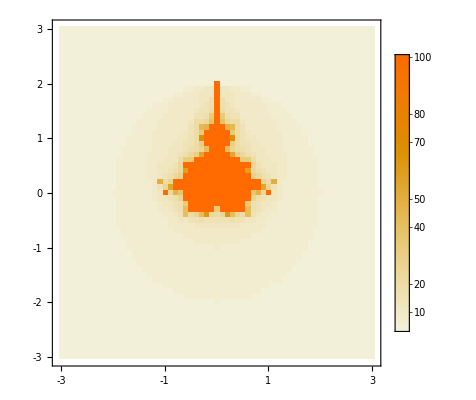

```mathematica
EscapeCount[c_]:=Module[
{z=0.0,n=0, zMax=2.0, nMax=100},
While[And[n++<nMax,Abs[z]<=zMax],z=z^2+c];
n]
cMax=3; Δc=0.1;
Data=Table[EscapeCount[x+ⅈ y],{x, -cMax,cMax,Δc},{y,-cMax,cMax,Δc}];
MatrixForm[Data];
MatrixPlot[Data,
PlotLegends->Automatic,
DataRange->cMax{{-1,1},{-1,1}}]
```

{6.07813,Null}

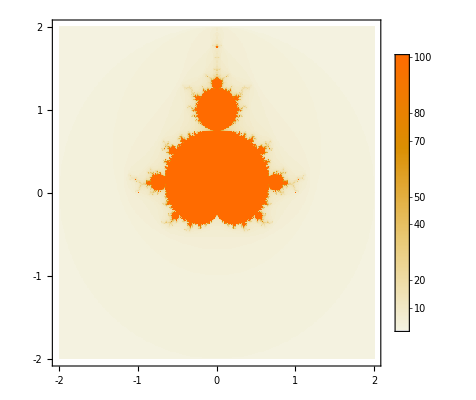

```mathematica
cMax=2; Δc=0.01;
AbsoluteTiming[
Data=Table[EscapeCount[x+ⅈ y],{x, -cMax,cMax,Δc},{y,-cMax,cMax,Δc}];
]
MatrixForm[Data];
MatrixPlot[Data,
PlotLegends->Automatic,
DataRange->cMax{{-1,1},{-1,1}}]
```